```mathematica
m=1;
g=7;
l=1;
```

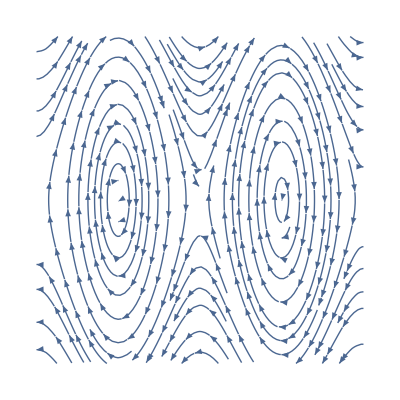

```mathematica
StreamPlot[{p/(m l^2),m g l Sin[θ]},{θ,-2π,2π},{p,-5,5},StreamColorFunction->None,StreamStyle->None,AspectRatio->1,Frame->False]
```

```mathematica
solpend[θc_,pc_]:=NDSolve[{p'[t]==m g l Sin[θ[t]],θ'[t]==p[t]/(m l^2),θ[0]==θc,p[0]==pc},{θ,p},{t,0,60}];
```

```mathematica
Reduce[p^2/(2m l^2)-m g l Cos[θ]<m g l]/.θ->π/2//N
```

-3.74166<p<3.74166

```mathematica
c1=ParametricPlot[Evaluate[{θ[t],p[t]}/. solpend[π/2,2]],{t,0,30},PlotRange->All];
```

```mathematica
Reduce[p^2/(2m l^2)-m g l Cos[θ]==m g l]/.θ->π/2//N
```

p==-3.74166||p==3.74166

```mathematica
c2=ParametricPlot[Evaluate[{θ[t],p[t]}/. solpend[π/2,3.7416573867739413]],{t,0,30},PlotRange->All];
```

```mathematica
Reduce[p^2/(2m l^2)-m g l Cos[θ]>m g l]/.θ->-π/2//N
```

p∈ℝ&&(p<-3.74166||p>3.74166)

```mathematica
c3=ParametricPlot[Evaluate[{θ[t],p[t]}/. solpend[-π/2,5]],{t,0,30}];
```

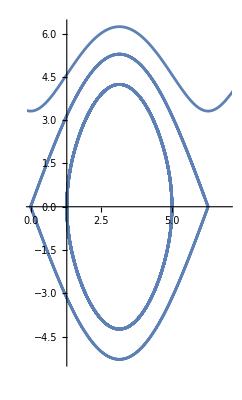

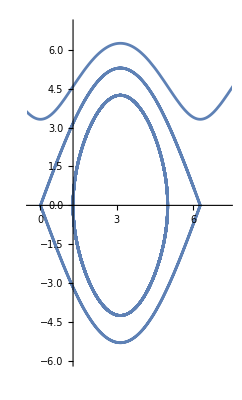

```mathematica
fullplot=Show[c1,c2,c3,PlotRange->{{0,7},All}]
```

```mathematica
{{1.734,4.056}}
```

{{1.734,4.056}}

```mathematica
Evaluate[p[t]/. solpend[0.8285,2.13]]
```

{InterpolatingFunction[…][t]}

We choose the point  in separatrix. Then, we choose two points slightly above and below separatrix regions by

```mathematica
ϵ=0.02;
```

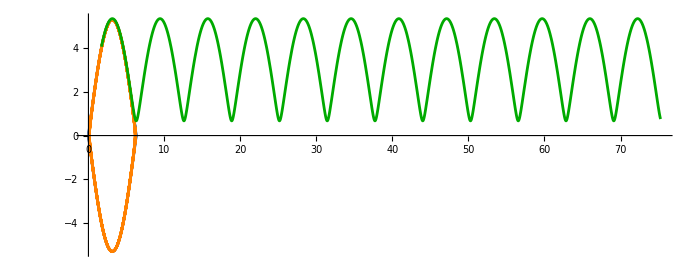

```mathematica
Show[c2,ParametricPlot[Evaluate[{θ[t],p[t]}/. solpend[1.734+ϵ,4.056]],{t,0,30},PlotRange->All,PlotStyle->Orange],ParametricPlot[Evaluate[{θ[t],p[t]}/. solpend[1.734-ϵ,4.056]],{t,0,30},PlotRange->All,PlotStyle->Darker[Green]],PlotRange->All,ImageSize->700]
```

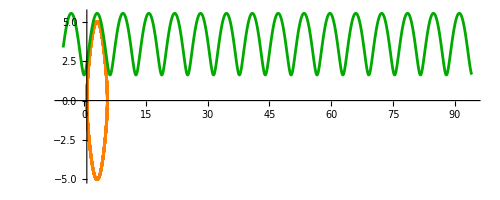

```mathematica
Show[ParametricPlot[Evaluate[{θ[t],p[t]}/. solpend[4.7,3.37]],{t,0,30},PlotRange->All,PlotStyle->Orange],ParametricPlot[Evaluate[{θ[t],p[t]}/. solpend[-5.1,3.37]],{t,0,30},PlotRange->All,PlotStyle->Darker[Green]]]
```

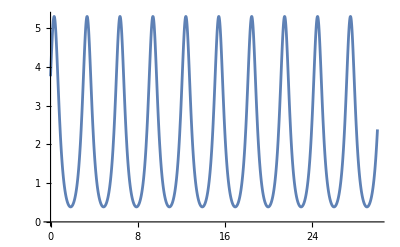

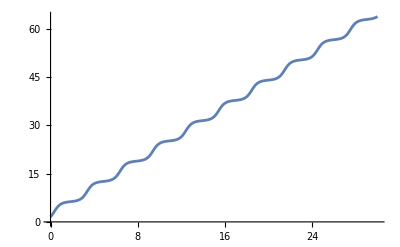

```mathematica
Plot[Evaluate[p[t]/. solpend[π/2,3.7416573867739413+ϵ]],{t,0,30}]
Plot[Evaluate[θ[t]/. solpend[π/2,3.7416573867739413+ϵ]],{t,0,30}]
```

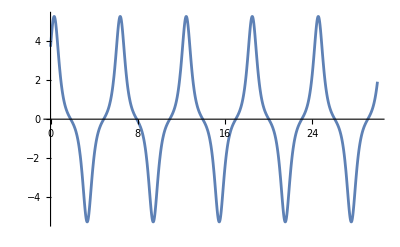

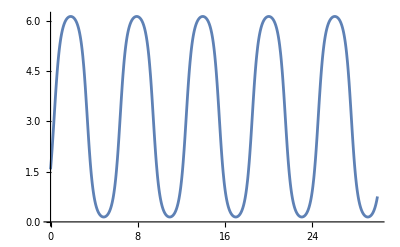

```mathematica
Plot[Evaluate[p[t]/. solpend[π/2,3.7416573867739413-ϵ]],{t,0,30}]
Plot[Evaluate[θ[t]/. solpend[π/2,3.7416573867739413-ϵ]],{t,0,30}]
```

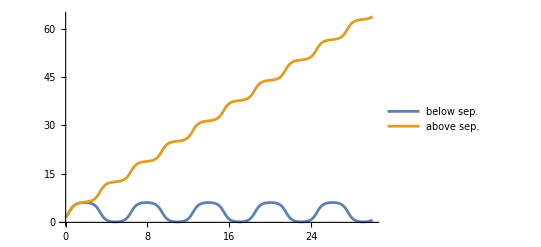

```mathematica
Plot[{Evaluate[θ[t]/. solpend[π/2,3.7416573867739413-ϵ]],Evaluate[θ[t]/. solpend[π/2,3.7416573867739413+ϵ]]},{t,0,30},PlotLegends->{"below sep.","above sep."},AxesLabel->{"",""},PlotRange->All]
```

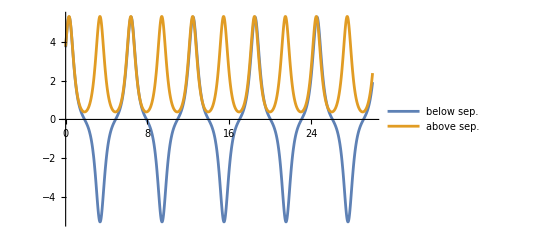

```mathematica
Plot[{Evaluate[p[t]/. solpend[π/2,3.7416573867739413-ϵ]],Evaluate[p[t]/. solpend[π/2,3.7416573867739413+ϵ]]},{t,0,30},PlotLegends->{"below sep.","above sep."},AxesLabel->{"",""},PlotRange->All]
```

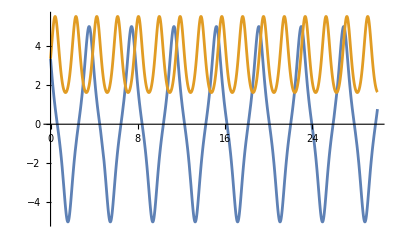

```mathematica
Plot[{Evaluate[p[t]/. solpend[4.7,3.37]],Evaluate[p[t]/. solpend[-5.1,3.37]]},{t,0,30}]
```